```mathematica
Phi[x_,xI_,dx_]=Piecewise[{{1-RealAbs[x-xI]/dx, RealAbs[x-xI]<dx}, {0, true}}]
```

```mathematica
Piecewise[{{1-RealAbs[x-xI]/dx, RealAbs[x-xI]<dx}, {0, True}}]
```

```mathematica
Plot3D[Phi[0,xI,1]Phi[0,yI,1],{xI,-2,2},{yI,-2,2},PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[Phi[0,xI,1]Phi[0,yI,1]
+Phi[0,xI+1,1]Phi[0,yI+1,1]
+Phi[0,xI,1]Phi[0,yI+1,1]
,{xI,-2,2},{yI,-2,2},PlotRange->Full]
```

-Graphics3D-

```mathematica
Grad[Phi[x,xI,h]Phi[y,yI,h],{xI,yI}]
Grad[Phi[0,xI,1]Phi[0,yI,1],{xI,yI}]/.{xI->.5,yI->.2}
```

```mathematica
{(Piecewise[{{1-RealAbs[y-yI]/h, RealAbs[y-yI]<h}, {0, True}}]) (Piecewise[{{1/h, x-xI≥0&&h-x+xI>0}, {-1/h, (x-xI≥0&&h-x+xI>0)||(x-xI<0&&h+x-xI>0)}, {0, True}}]),(Piecewise[{{1-RealAbs[x-xI]/h, RealAbs[x-xI]<h}, {0, True}}]) (Piecewise[{{1/h, y-yI≥0&&h-y+yI>0}, {-1/h, (y-yI≥0&&h-y+yI>0)||(y-yI<0&&h+y-yI>0)}, {0, True}}])}
```

{-0.8,-0.5}

```mathematica
VectorPlot[Grad[Phi[0,xI,1]Phi[0,yI,1],{xI,yI}]/.{xI->x,yI->y},{x,-2,2},{y,-2,2},PlotRange->Full]
```

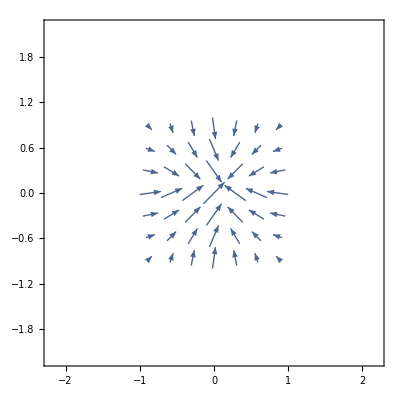

```mathematica
dx0 = 1/(128*3)
.25dx0
.75 dx0

{Phi[0,xI,dx0]Phi[0,yI,dx0],
Grad[Phi[0,xI,dx0]Phi[0,yI,dx0],{xI,yI}]}/.{xI->-.25dx0,yI->-.75dx0}
```

1/384

0.000651042

```mathematica
0.001953125
```

{0.1875,{96.,288.}}

```mathematica
0.0006510416666666666
```

0.00195313

```mathematica
{0.1875,{96.,288.}}
```

```mathematica
Table[
Grad[Phi[0.75dx0,xI,dx0]Phi[0.75dx0,yI,dx0],{xI,yI}]/.{xI->f*dx0,yI->g*dx0},{f,0,3},{g,0,3}]//MatrixForm
```

((96.
96.) | (288.
-96.) | (0.
0.) | (0.
0.)
(-96.
288.) | (-288.
-288.) | (0.
0.) | (0.
0.)
(0.
0.) | (0.
0.) | (0
0) | (0
0)
(0.
0.) | (0.
0.) | (0
0) | (0
0))

```mathematica
ListVectorPlot[Table[{{x/2,y/2},Grad[Phi[.75,xI,1]Phi[0.75,yI,1],{xI,yI}]}/.{xI->x/2,yI->y/2},{x,0,3},{y,0,3}],PlotRange->Full]
```

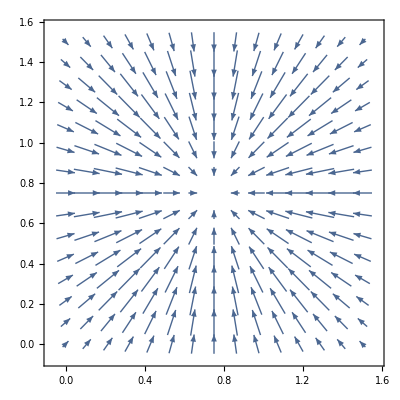

```mathematica
(* should be equivalent to W_grad_x_grid_offset
*)Table[(Grad[Phi[0.75dx0,xI,dx0]Phi[0.75dx0,yI,dx0],{xI,yI}]/.{xI->dx0 x/2,yI->dx0 y/2}),{x,0,3},{y,0,3}][[All,All,1]]//MatrixForm


(* should be equivalent to W_grad_y_grid_offset
*)
Table[Grad[Phi[0.75dx0,xI,dx0]Phi[0.75dx0,yI,dx0],{xI,yI}]/.{xI->dx0 x/2,yI->dx0 y/2},{x,0,3},{y,0,3}][[All,All,2]]//MatrixForm

(*These do indeed match*)
```

(96. | 288. | 288. | 96.
96. | 288. | 288. | 96.
-96. | -288. | -288. | -96.
-96. | -288. | -288. | -96.)

(96. | 96. | -96. | -96.
288. | 288. | -288. | -288.
288. | 288. | -288. | -288.
96. | 96. | -96. | -96.)